[-Graphics-](https://github.com/Eltaurus-Lt/CnC/tree/main/Scripts)[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive

# Определения и предварительные примеры

```mathematica
eq=z^3-1; (*правая часть уравнения eq=0*)
iteration=((#-eq/D[eq,z])/.z->#)&; (*итерация метода Ньютона Subscript[z, n]->Subscript[z, n+1]*)
```

```mathematica
(*пара итераций от заданных начальных условий*)
iteration@iteration@(3.+ⅈ)
```

1.41115+0.38845 ⅈ

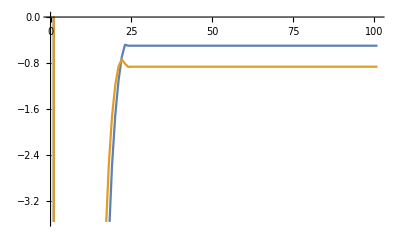

```mathematica
list1=NestList[iteration,.003+0.01ⅈ,100];
ListLinePlot[ReIm[list1]ᵀ] (*пример динамики действительной и мнимой частей агрумента при многократном итерировании - видна сходимость за ~25 шагов к корню -1/2-√3 ⅈ/2*)
```

# Построение диаграммы

```mathematica
a=2; (*половина стороны изображаемой квадратной области*)
res=200; (*разрешение, px*)
z0=Table[re+ⅈ im,{im,a(1-1/res),-a(1-1/res),-(2a)/res},{re,-a(1-1/res),a(1-1/res),(2a)/res}]; (*квадратная сетка из координат центров пикселей на комплексной плоскости (двумерный массив минмых чисел)*)
roots=N[z/.Solve[eq==0,z]]; (*множество корней уравнения*)

(*функция окрашивания мнимых чисел:*)
color[z_]:=(colorset={RGBColor[0.01568627450980392, 0.76, 0.14],RGBColor[0.9490196078431372, 1, 0.91],RGBColor[0.1, 0.17, 0.18]};(*набор цветов (количество должно быть равно количеству коррней roots)*)
C∞=ComplexInfinity;If[Count[#,C∞]>0,colorset⟦Position[#,C∞]⟦1,1⟧⟧(*функция окрашивания в случае близости к одному из корней*),Blend[colorset,#](*функция окрашивания в случае общего положения - взвешенная сумма цветов из colorset*)]&@(Max[#,10^-10]^-1(*веса каждого из корней в определении цвета минмого числа*)&/@Abs[z-roots]));
```

```mathematica
(*примеры окрашивания чисел*)
color[1]
color/@{ⅈ,0,-ⅈ,-2+ⅈ}
```

RGBColor[0.0156862745685578, 0.7599999999797927, 0.14000000004676535]

{RGBColor[0.22034039777488493, 0.43827394928043356, 0.2907495151653316],RGBColor[0.3549019607843137, 0.6433333333333333, 0.41000000000000003],RGBColor[0.6007168681330481, 0.8101292839284948, 0.6178030022654336],RGBColor[0.33460164804640496, 0.5514560999331227, 0.3890646264449442]}

```mathematica
(*окрашивание исходной комплексной плоскости - центры цветовых пятен соответствуют трём корням уравнения*)
Image@Map[color,z0,{2}]
```

-Graphics-

```mathematica
(*окрашивание комплексной плоскости после 5 итераций метода Ньютона*)
z5=Quiet@Map[Nest[iteration,N[#],5]&,z0,{2}];
Image@Map[color,z5,{2}]
```

-Graphics-

```mathematica
(*Бассейны Ньютона - предельная картина после большого числа итераций (необходимое число можно оценить по графику в первом разделе)*)
z∞=Quiet@Map[Nest[iteration,N[#],50]&,z0,{2}];
Image@Map[color,z∞,{2}]
```

-Graphics-

# Анимация последовательных итераций

```mathematica
Pic[n_Integer?(!Negative[#]&)]:=Image[Map[color,Quiet@Map[Nest[iteration,N[#],n]&,z0,{2}],{2}]];
```

*код может быть значительно оптимизирован, если вместо рисования каждого отдельного кадра с нуля будет реализован предвариательный расчет всех итераций до максимальной нужной глубины с сохранением результатов промежуточных шагов

```mathematica
animationname="Newton Basins";
SetDirectory@NotebookDirectory[];
Quiet@CreateDirectory[animationname<>" frames"];

(*экспорт в последовательность png-кадров*)
Export[animationname<>" frames\\"<>StringPadLeft[ToString[#],3,"0"]<>".png",Pic[#],"png"]&/@Range[0,25];
```